```mathematica
Read data and make functions
```

```mathematica
(*Convert datetime series to normal series starting "start" year*)
SetDirectory[NotebookDirectory[]];

FF[x_,start_,incr_]:=
(
new={};
For[i=1,i≤Length[x],i++,
new=Append[new,{start+(i-1)*incr,x[[i]][[2]]}]];
Return[new];
)
(*reverse*)
FF2[x_,start_,incr_]:=
(

new={};
For[i=1,i≤Length[x],i++,
new=Append[new,{start-(i-1)*incr,x[[i]][[2]]}]];
Return[new];
)
(*Take date timeseries and convert to only monthly data*)
GG[x_]:=(new={x[[1]]};
For[i=2,i≤Length[x],i=i+1,
If[DateValue[x[[i-1]][[1]],"Month"]!=DateValue[x[[i]][[1]],"Month"],
new=Append[new,{x[[i]][[1]],x[[i]][[2]]}]
]
];
Return[new];
)
```

```mathematica
data1=Import["gold_price.csv"];
data2=Import["silver_price.csv"];
gold=data1[[456;;]];(*Starting 1970, gold price*)

silver=data2[[672;;,{1,2}]];(*starting 1970, silver price*)

gold2={};
gold2=Append[gold2,gold[[1]]];c=1;
gold2=GG[gold];
gold=gold2;

inflation=Import["inflation.csv"][[392;;,{3,4}]];
silver2={};inf=1;For[i=Length[silver]-1,i≥1,i--,
silver2=Append[silver2,{silver[[i]][[1]],inf*silver[[i]][[2]]}];
inf=inf/(1+inflation[[i]][[2]]/1200);
]
silver=Reverse[silver2];
Inflation[gold_,inflation_]:=(
goldinfl={};
inf=1;
For[i=Length[gold]-1,i≥1,i--,
goldinfl=Append[goldinfl,{gold[[i]][[1]],inf*gold[[i]][[2]]}];
inf=inf/(1-inflation[[i]][[2]]/1200);];
goldinfl=Reverse[goldinfl];
Return[goldinfl];
)
```

```mathematica
Inflation[gold_,inflation_]:=(
goldinfl={};
inf=1;
For[i=Length[gold]-1,i≥1,i--,
goldinfl=Append[goldinfl,{gold[[i]][[1]],inf*gold[[i]][[2]]}];
inf=inf/(1-inflation[[i]][[2]]/1200);];
goldinfl=Reverse[goldinfl];
Return[goldinfl];
)
```

```mathematica
silver;
```

```mathematica
cpi=Import["CPI.csv"][[240;;,{3,4}]];(*Data from 1970*)


rate=Import["interest_rate.csv"][[2;;,{3,4}]];
rate=GG[rate];

monetary=Import["monetary_base.csv"][[134;;,{2,3}]];

snp=Import["snp_index.csv"][[507;;,{1,2}]];

pe=Import["snp_pe.csv"][[522;;]];

gsci=Import["gsci.csv"][[2;;,{2,3}]];
gsci=GG[gsci];
gsci=Reverse[gsci];

yield=Import["Treasury_yield.csv"];
yield=GG[yield];
For[i=10,i≤Length[yield]-1,i++,
If[yield[[i]][[2]]=="#N/A",yield[[i]][[2]]=yield[[i+1]][[2]];]];
yield=yield[[98;;]];
```

```mathematica
Make plots
```

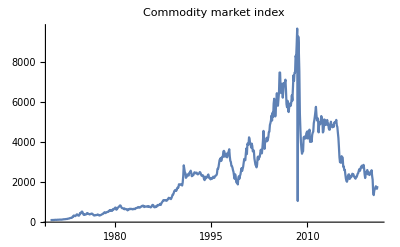

```mathematica
ListPlot[FF[gsci,1970,1/12],Joined->True,PlotLabel->"Commodity market index"]
```

```mathematica
(*Plot silver and gold price*)
```

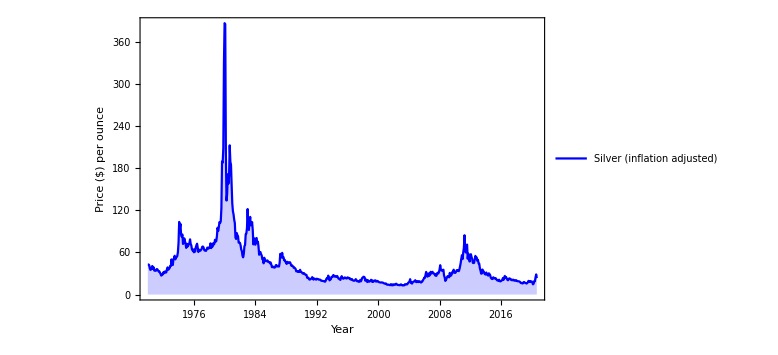
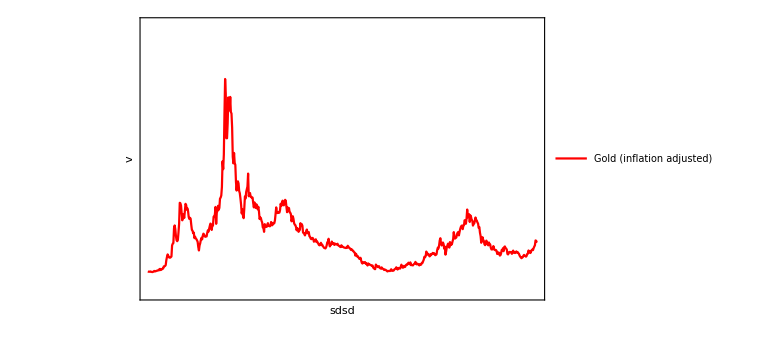

silver_gold_inflation.png

```mathematica
plot1=ListPlot[FF[Inflation[silver,realinfl],1970,1/12],PlotRange->All,PlotStyle->Blue,ImagePadding->50, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver (inflation adjusted)"},{.5,.8}],FrameLabel->{"Year","Price ($) per ounce"},ImageSize->Large,BaseStyle->14, Filling->Axis];
plot2=ListPlot[FF[Inflation[gold,realinfl],1970,1/12],PlotRange->{0,10000},PlotStyle->Red,Axes->False,ImagePadding->50,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},14],Joined->True,PlotLegends->Placed[{"Gold (inflation adjusted)"},{.5,.7}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->14];
comb=Overlay[{plot1,plot2}]
Export["silver_gold_inflation.png",comb]
```

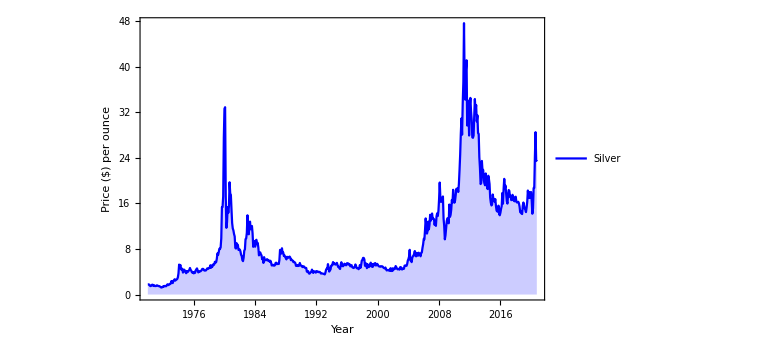
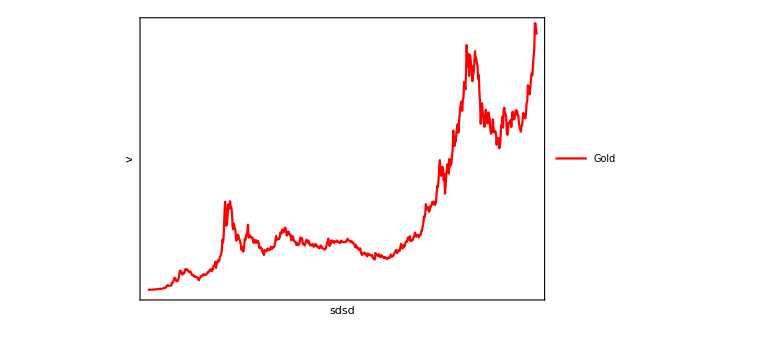

silver_gold.png

```mathematica
plot1=ListPlot[FF[silver,1970,1/12],PlotRange->All,PlotStyle->Blue,ImagePadding->50, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver"},{.5,.8}],FrameLabel->{"Year","Price ($) per ounce"},ImageSize->Large,BaseStyle->14,Filling->Axis];
plot2=ListPlot[FF[gold,1970,1/12],PlotStyle->Red,Axes->False,ImagePadding->50,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},14],Joined->True,PlotLegends->Placed[{"Gold"},{.5,.7}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->14];
comb=Overlay[{plot1,plot2}]
Export["silver_gold.png",comb]
```

```mathematica
(*Plot correlation between silver and gold price*)
```

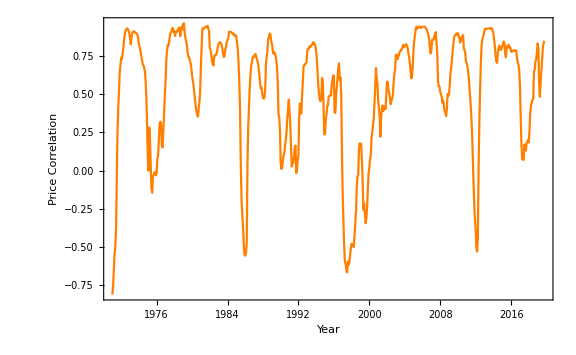

silver_gold_corr.png

```mathematica
s1=FF[silver,1970,1/12];
s2=FF[gold,1970,1/12];
corr={};
num=24;
For[i=1,i≤Length[s1]-num,i++,
corr=Append[corr,{s1[[i+num/2]][[1]],Correlation[s1[[i;;i+num,2]],s2[[i;;i+num,2]]]}]]
plotcorr=ListPlot[corr,Joined->True,PlotRange->All,PlotStyle->Orange, Frame->True,Frame->True,FrameStyle->Directive[Black,14],Joined->True,FrameLabel->{"Year","Price Correlation"},ImageSize->Large,BaseStyle->14]
Export["silver_gold_corr.png",plotcorr]
```

```mathematica
(*Silver/Gold ratio vs SnP 500*)
```

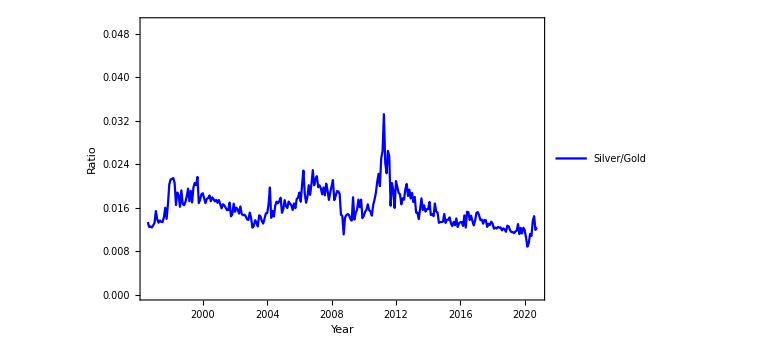
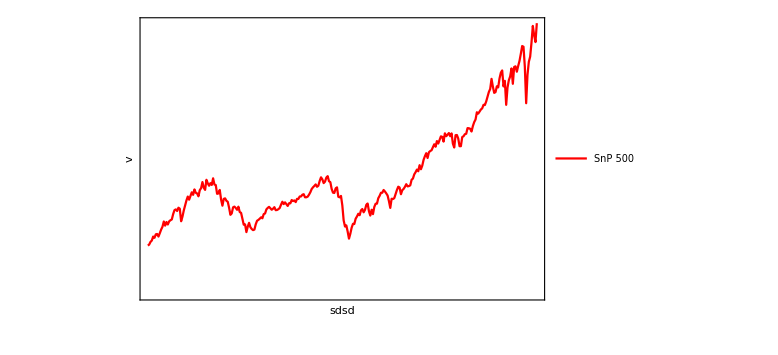

```mathematica
f[x_]:=0;
ratio=Array[f,{Length[s1],2}];
For[i=1,i≤Length[s1],i++,
ratio[[i]][[1]]=s1[[i]][[1]];
ratio[[i]][[2]]=s1[[i]][[2]]/s2[[i]][[2]];]

plot1=ListPlot[ratio[[320;;]],PlotRange->{0,0.05},PlotStyle->Blue,ImagePadding->74, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver/Gold"},{.5,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16];
plot2=ListPlot[FF[snp,1970,1/12][[320;;]],PlotStyle->Red,Axes->False,ImagePadding->74,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},16],Joined->True,PlotLegends->Placed[{"SnP 500"},{.5,.75}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->16];
comb=Overlay[{plot1,plot2}]
Export["silver_gold_snp_comp.png",comb]
```

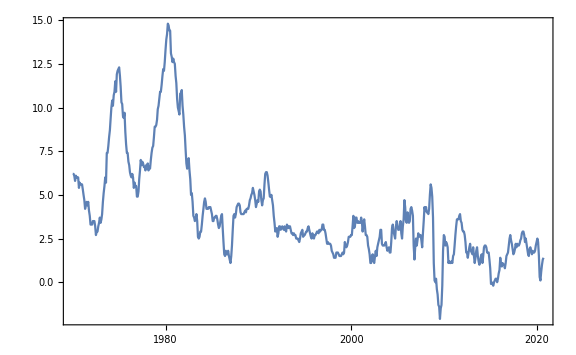

```mathematica
DateListPlot[inflation]
```

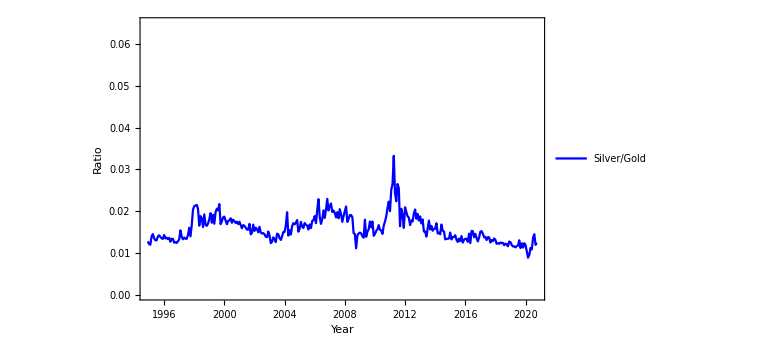
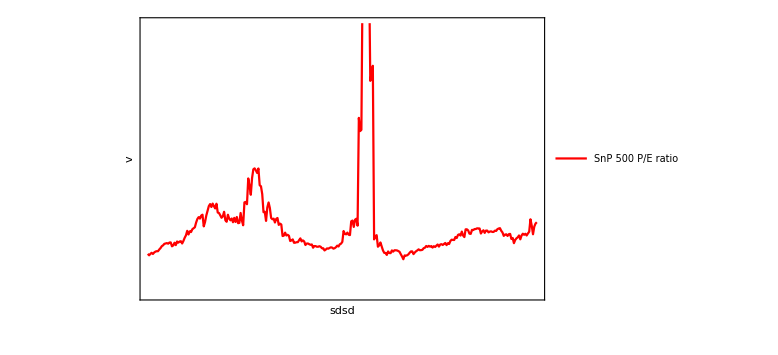

silver_gold_snp_pe.png

```mathematica
plot1=ListPlot[ratio[[300;;]],PlotRange->{0,0.065},PlotStyle->Blue,ImagePadding->74, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver/Gold"},{.8,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16];
plot2=ListPlot[FF[pe,1970,1/12][[300;;]],PlotRange->{0,100},PlotStyle->Red,Axes->False,ImagePadding->74,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},16],Joined->True,PlotLegends->Placed[{"SnP 500 P/E ratio"},{.8,.75}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->16];
comb=Overlay[{plot1,plot2}]
Export["silver_gold_snp_pe.png",comb]
```

```mathematica
s3;
```

```mathematica
s1
```

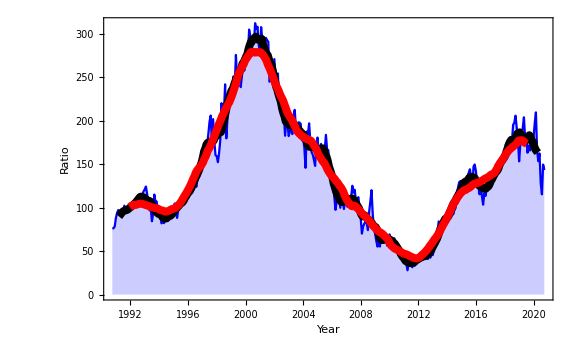

Snp_500_silver_ratio.png

```mathematica
s3=FF[snp,1970,1/12]; (*SnP data*)
f[x_]:=0;
ratio2=Array[f,{Length[s1],2}];
For[i=1,i≤Length[s1],i++,
ratio2[[i]][[1]]=s1[[i]][[1]];
ratio2[[i]][[2]]=s3[[i]][[2]]/s1[[i]][[2]];]
plot1=ListPlot[{ratio2[[250;;]]},PlotRange->All,PlotStyle->{{Blue},{Red,Thickness[0.005]}},ImagePadding->74, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"(SnP 500)/Silver"},{.7,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16,Filling->{Axis}];
plot2=ListPlot[{MovingAverage[ratio2[[250;;]],12],MovingAverage[ratio2[[250;;]],30]},PlotRange->All,PlotStyle->{{Black,Thickness[.01]},{Red,Thickness[0.01]}},ImagePadding->74, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"MA(1 yr)","MA(2.5 yrs)"},{.7,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16,Filling->{Axis,None,None}];plotter=Show[plot1,plot2]
Export["Snp_500_silver_ratio.png",plotter]
```

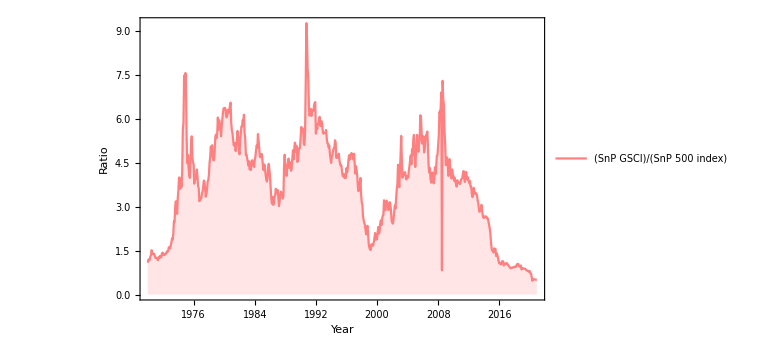

```mathematica
s3=FF[snp,1970,1/12];
s4=FF[gsci,1970,1/12]; (*Gsci data*)
f[x_]:=0;
ratio2=Array[f,{Length[s3],2}];
For[i=1,i≤Length[s3],i++,
ratio2[[i]][[1]]=s3[[i]][[1]];
ratio2[[i]][[2]]=s4[[i]][[2]]/s3[[i]][[2]];]
plot1=ListPlot[ratio2[[1;;]],PlotRange->All,PlotStyle->Pink,ImagePadding->74, Frame->{{True,True},{True,True}},Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"(SnP GSCI)/(SnP 500 index)"},{.7,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16,Filling->Axis]
Export["gsci_snp_500_ratio.png",plot1]
```

```mathematica
Predictions
```

gsci_snp_500_ratio.png

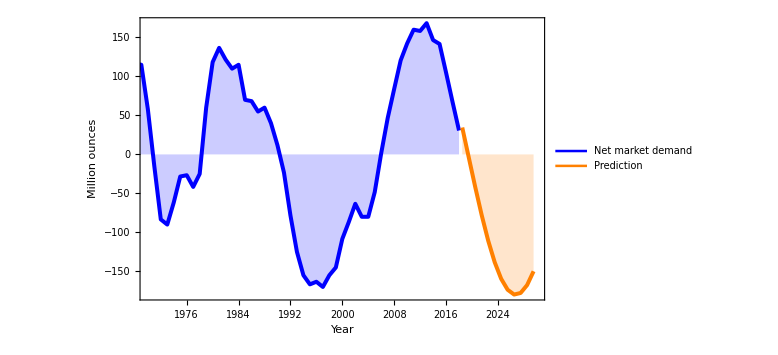

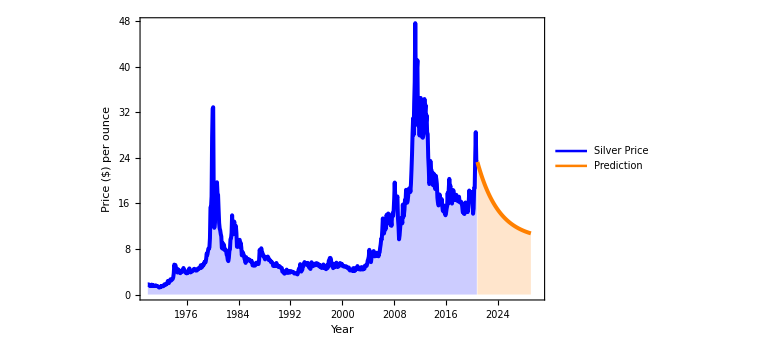

```mathematica
SetDirectory[NotebookDirectory[]];

data=FF[silver,1970,1/12][[1;;]];
eproc=EstimatedProcess[data,ARMAProcess[2,1]];
forecast=TimeSeriesForecast[eproc,data,{100}];
ListPlot[{data,forecast},Joined->True,Filling->Bottom]

silverinvest=Import["silver_investment_demand.xlsx"][[1]];
silverinvest1=Table[{silverinvest[[i]][[1]],silverinvest[[i]][[2]]},{i,1,Length[silverinvest]}];
avg=3;
mylist=MovingAverage[silverinvest1,avg];
mylist2=Table[{mylist[[i]][[1]],mylist[[i]][[2]]},{i,1,Length[mylist]}];
func=Piecewise[{{95*Sin[(x-1963)/2.34],(x-1963)<14.7},{110*Sin[.6((x-1963)-14.7)/2.34],27>(x-1963)>14.7},{-150*Sin[.5((x-1963)-27)/2.34],41.7>(x-1963)>27},{150*Sin[.5((x-1963)-41.7)/2.34],(x-1963)>41.7}}];
mylist3=Table[{i,1.2func/.x->i},{i,2018.5,2030,1}];

plot1=ListPlot[{mylist2,mylist3},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Net market demand","Prediction"},{.47,.85}],FrameLabel->{"Year","Million ounces"},ImageSize->Large,BaseStyle->16,PlotRange->{{1970,2030},All},Filling->Axis]

plot2=ListPlot[{data,forecast},ImagePadding->74,Frame->True,FrameTicks->{{All,None},{All,None}},FrameStyle->Directive[{{Automatic,Black},{Automatic,Black}},16],PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]}},Joined->True,PlotLegends->Placed[{"Silver Price","Prediction"},{.5,.75}],FrameLabel->{"Year","Price ($) per ounce"},ImageSize->Large,BaseStyle->16,PlotRange->{{1970,2030},All},Filling->Bottom]
```

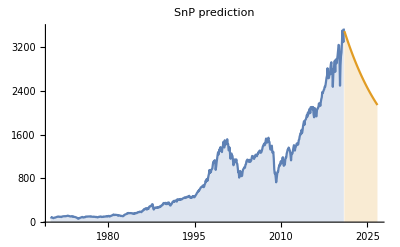

```mathematica
data=FF[snp,1970,1/12][[1;;]];
eproc=EstimatedProcess[data,ARMAProcess[2,1]];
forecast=TimeSeriesForecast[eproc,data,{70}];
ListPlot[{data,forecast},Joined->True,Filling->Bottom,PlotLabel->"SnP prediction"]
```

```mathematica
data=ratio2[[200;;]];
eproc=EstimatedProcess[data,ARMAProcess[2,1]];
forecast=TimeSeriesForecast[eproc,data,{70}];
ListPlot[{data,forecast},Joined->True,Filling->Bottom,PlotRange->All,"SnP/Silver"]
```

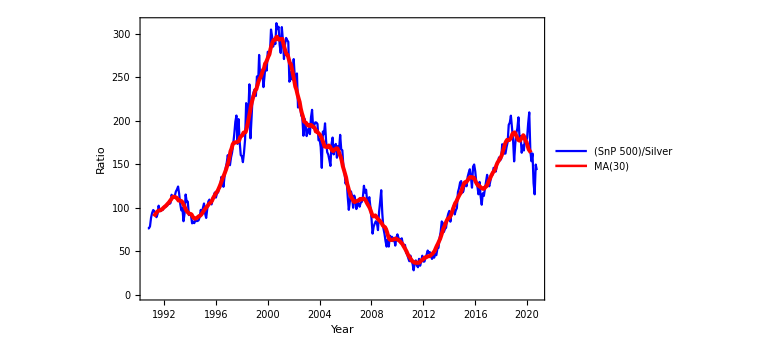

```mathematica
s3=FF[snp,1970,1/12]; (*SnP data*)
f[x_]:=0;
ratio2=Array[f,{Length[s1],2}];
For[i=1,i≤Length[s1],i++,
ratio2[[i]][[1]]=s1[[i]][[1]];
ratio2[[i]][[2]]=s3[[i]][[2]]/s1[[i]][[2]];]
plot1=ListPlot[{ratio2[[250;;]],MovingAverage[ratio2[[250;;]],12]},PlotRange->All,PlotStyle->{{Blue},{Red,Thickness[0.005]}},ImagePadding->74, Frame->True,Frame->True,FrameStyle->Blue,Joined->True,PlotLegends->Placed[{"(SnP 500)/Silver","MA(30)"},{.7,.85}],FrameLabel->{"Year","Ratio"},ImageSize->Large,BaseStyle->16]
```

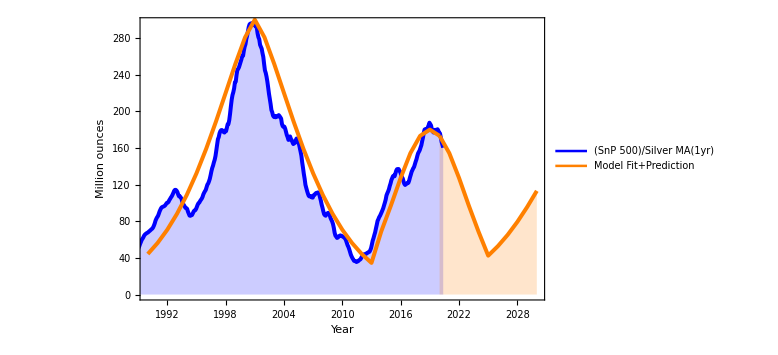

Snp_silver_forecast.png

```mathematica
avg=10;
mylist=MovingAverage[ratio2,avg];
mylist2=Table[{mylist[[i]][[1]],mylist[[i]][[2]]},{i,220,Length[mylist]}];
n1=1.4;
b1=15;
n2=2;
b2=26;
n3=1.4;
b3=15;
func=Piecewise[{{250*Exp[-(2001-x)^n1/b1],(x-2001)<0},{250*Exp[-(x-2001)^n1/b1],0<=(x-2001)<13},{150*Exp[-(2019-x)^n2/b2],(x-2019)<=0},{150*Exp[-(x-2019)^n2/b2],5>=(x-2019)>0},{150*Exp[-(2034-x)^n3/b3],(x-2034)<0}}];
(*func=Piecewise[{{250/(x-2001)^2,(x-1963)<50},{150*Sin[.5((x-1963)-41.7)/2.34],(x-1963)>50}}];
*)mylist3=Table[{i,1.2func/.x->i},{i,2020,2030,1}];

plot1=ListPlot[{mylist2,mylist3},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"(SnP 500)/Silver MA(1yr)","Model Fit+Prediction"},{.67,.85}],FrameLabel->{"Year","Million ounces"},ImageSize->Large,BaseStyle->16,PlotRange->{{1990,2030},All},Filling->Axis];
mylist3=Table[{i,1.2func/.x->i},{i,1990,2020,1}];

plot2=ListPlot[{mylist3},PlotStyle->{{Orange,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,FrameLabel->{"Year","Million ounces"},ImageSize->Large,BaseStyle->16,PlotRange->{{1990,2030},All}];
Show[plot1,plot2]
Export["Snp_silver_forecast.png",Show[plot1,plot2]]
```

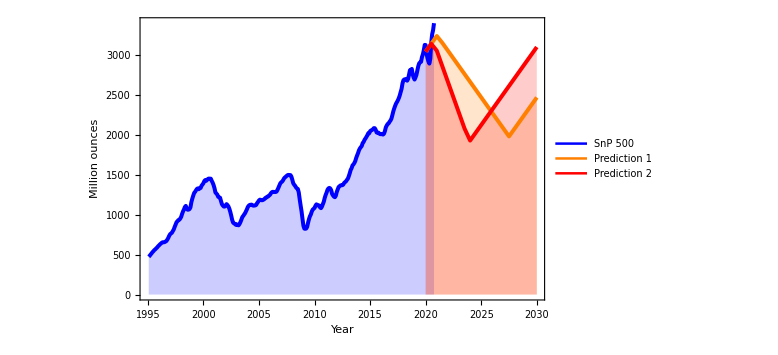

snp_projection.png

```mathematica
f[x_]:=0;
ratio=Array[f,{Length[s1],2}];
For[i=1,i≤Length[s1],i++,
ratio[[i]][[1]]=s1[[i]][[1]];
ratio[[i]][[2]]=s1[[i]][[2]]/s2[[i]][[2]];]

avg=5;
mylist=MovingAverage[FF[snp,1970,1/12],avg];
mylist2=Table[{mylist[[i]][[1]],mylist[[i]][[2]]},{i,300,Length[mylist]}];

func1=Piecewise[{{150(x-1995)+400,1995<=x<=2000.5},{-150(x-1995)+2000,2000.5<=x<=2003},{100(x-1995),2003<=x≤2008},{-300(x-1995)+5200,2008<=x<=2009.5},{170(x-1995)-1600,2009.5<=x≤2021},{-170(x-1995)+7250,2021<=x≤2027},{170(x-1995)-3800,x>2027}}];
func2=Piecewise[{{150(x-1995)+400,1995<=x<=2000.5},{-150(x-1995)+2000,2000.5<=x<=2003},{100(x-1995),2003<=x≤2008},{-300(x-1995)+5200,2008<=x<=2009.5},{170(x-1995)-1600,2009.5<=x≤2020.5},{-340(x-1995)+11500,2020.5<=x≤2023.5},{170(x-1995)-3250,x>2023.5}}];
(*func=Piecewise[{{250/(x-2001)^2,(x-1963)<50},{150*Sin[.5((x-1963)-41.7)/2.34],(x-1963)>50}}];
*)mylist3=Table[{i,1.15func1/.x->i},{i,2020,2030,0.5}];
mylist4=Table[{i,1.15func2/.x->i},{i,2020,2030,0.5}];
plot1=ListPlot[{mylist2,mylist3,mylist4},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Red,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"SnP 500","Prediction 1","Prediction 2"},{.47,.8}],FrameLabel->{"Year","Million ounces"},ImageSize->Large,BaseStyle->16,PlotRange->{{1995,2030},All},Filling->Axis]
Export["snp_projection.png",plot1]
```

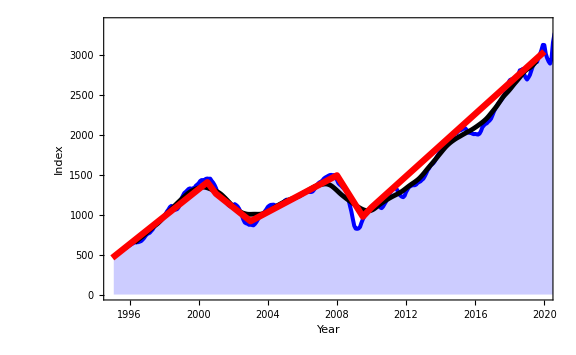

snp_fit.png

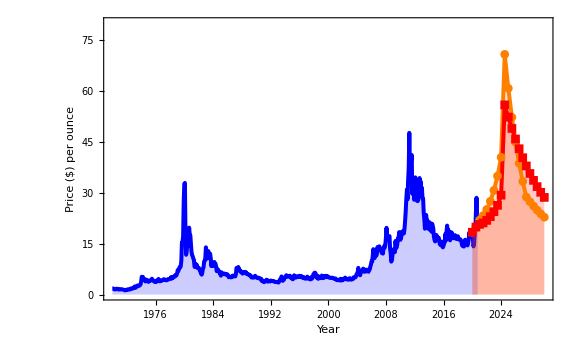

silver_market_cycle_forecast.png

```mathematica
mylist3=Table[{i,1.15func1/.x->i},{i,1995,2020,0.5}];
mylist4=Table[{i,1.15func2/.x->i},{i,1995,2020,0.5}];
plot1=ListPlot[{mylist2},PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Red,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"SnP 500","Prediction 1","Prediction 2"},{.47,.8}],FrameLabel->{"Year","Index"},ImageSize->Large,BaseStyle->16,PlotRange->{{1995,2020},All},Filling->Axis];
plot2=ListPlot[{MovingAverage[mylist2,30],mylist3},PlotStyle->{{Black,Thickness[.006]},{Red,Thickness[.008]},{Red,Thickness[.005]}},ImagePadding->74,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"MA(2.5 yr)","Straight line fit"},{.47,.8}],FrameLabel->{"Year","Index"},ImageSize->Large,BaseStyle->16,PlotRange->{{1995,2020},All}];
Show[plot1,plot2]
Export["snp_fit.png",Show[plot1,plot2]]
predsilver1=Table[{i,(func1/func)/.x->i},{i,2020,2030,.5}];
predsilver2=Table[{i,(func2/func)/.x->i},{i,2020,2030,.5}];
data=FF[silver,1970,1/12][[1;;]];
plot1=ListPlot[{data},ImagePadding->74,Frame->True,FrameTicks->{{All,None},{All,None}},FrameStyle->Directive[{{Automatic,Black},{Automatic,Black}},16],PlotStyle->{{Blue,Thickness[.005]},{Orange,Thickness[.005]},{Red}},Joined->True,PlotLegends->Placed[{"Silver Price","Prediction1","Prediction2"},{.5,.75}],FrameLabel->{"Year","Price ($) per ounce"},ImageSize->Large,BaseStyle->16,PlotRange->{{1970,2030},{0,80}},Filling->Axis];
plot2=ListPlot[{predsilver1,predsilver2},ImagePadding->74,Frame->True,FrameTicks->{{All,None},{All,None}},FrameStyle->Directive[{{Automatic,Black},{Automatic,Black}},16],PlotStyle->{{Orange,Thickness[.005]},{Red,Thickness[.005]},{Red}},Joined->True,PlotLegends->Placed[{"Prediction1","Prediction2"},{.5,.75}],FrameLabel->{"Year","Price ($) per ounce"},ImageSize->Large,BaseStyle->16,PlotRange->{{1970,2030},All},PlotMarkers->Automatic,Filling->Axis];
Show[plot1,plot2]
Export["silver_market_cycle_forecast.png",Show[plot1,plot2]]
```

```mathematica
Silver demand(investment/jewelry/industry) history and correlation with prices
```

```mathematica
FF[silver,1970,1/12];
```

```mathematica
SetDirectory[NotebookDirectory[]];
jewellery=Import["Silver_demand.xlsx",{"Sheets","jewellery and silverware"}]
silvermonth=FF[silver,1970,1/12][[110;;]];
silveryear={};c=0;
For[i=1,i≤Length[silvermonth],i++,c=c+1;sum=sum+silvermonth[[i]][[2]];
If[c==12,silveryear=Append[silveryear,{IntegerPart[silvermonth[[i]][[1]]],sum/12}];
sum=0;
c=0;];]
rate=4;
jewelleryproj={{2021,jewellery[[Length[jewellery]]][[2]]*(1-rate/100)}};
For[i=2,i≤8,i++,
jewelleryproj=Append[jewelleryproj,{jewelleryproj[[i-1]][[1]]+1,jewelleryproj[[i-1]][[2]]*(1+rate/100)}]]
```

{{1980.,52.},{1981.,48.},{1982.,55.},{1983.,48.},{1984.,48.},{1985.,60.},{1986.,70.},{1987.,75.},{1988.,85.},{1989.,105.},{1990.,115.},{1991.,160.},{1992.,170.},{1993.,225.},{1994.,225.},{1995.,230.},{1996.,270.},{1997.,280.},{1998.,290.},{1999.,285.},{2000.,285.},{2001.,290.},{2002.,275.},{2003.,270.},{2004.,260.},{2005.,260.},{2006.,225.},{2007.,235.},{2008.,230.},{2009.,234.},{2010.,235.},{2011.,240.},{2012.,240.},{2013.,270.},{2014.,275.},{2015.,295.},{2016.,299.},{2017.,302.},{2018.,310.},{2019.,305.},{2020.,250.}}

```mathematica
jewelleryproj
```

{{2021,361.13},{2022,389.298},{2023,419.663},{2024,452.397},{2025,487.684},{2026,525.723},{2027,566.73},{2028,610.935}}

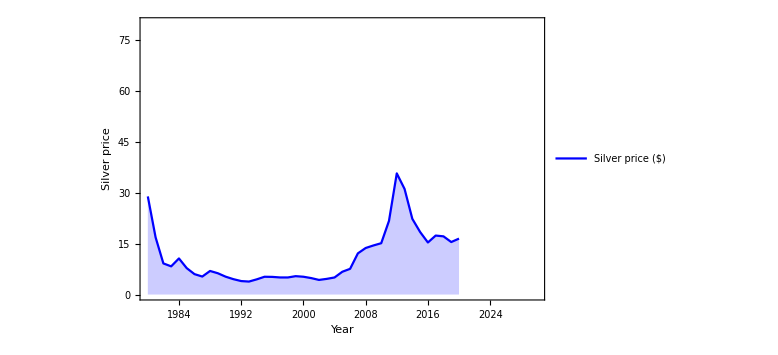
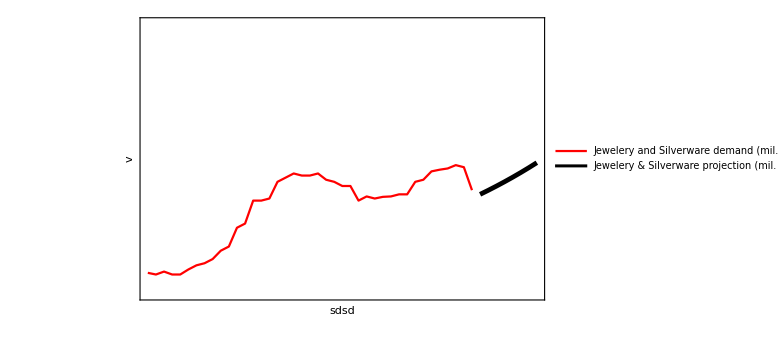

Jewelery_demand.png

```mathematica
plot1=ListPlot[silveryear,PlotRange->{{1980,2030},{0,80}},PlotStyle->Blue,ImagePadding->74, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver price ($)"},{.5,.92}],FrameLabel->{"Year","Silver price"},ImageSize->Large,BaseStyle->16,Filling->Axis];
plot2=ListPlot[{jewellery,jewelleryproj},PlotRange->{0,650},PlotStyle->{Red,{Black,Thickness[.006]}},Axes->False,ImagePadding->74,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},16],Joined->True,PlotLegends->Placed[{"Jewelery and Silverware demand (mil. oz)","Jewelery & Silverware projection (mil. oz)"},{.5,.75}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->16];
comb=Overlay[{plot1,plot2}]
Export["Jewelery_demand.png",comb]
```

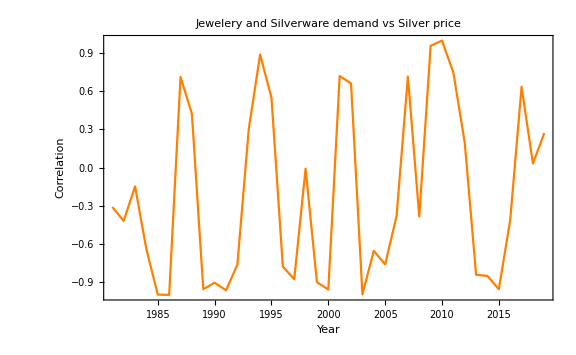

```mathematica
Corr[s1_,s2_,num_]:=(corr={};
For[i=1,i≤Length[s1]-num,i++,
corr=Append[corr,{s1[[i+num/2]][[1]],Correlation[s1[[i;;i+num,2]],s2[[i;;i+num,2]]]}]];
plotcorr=ListPlot[corr,Joined->True,PlotRange->All,PlotStyle->Orange, Frame->True,Frame->True,FrameStyle->Directive[Black,14],Joined->True,FrameLabel->{"Year","Correlation"},ImageSize->Large,BaseStyle->14,PlotLabel->"Jewelery and Silverware demand vs Silver price",BaseStyle->Black];
Return[plotcorr];)
Corr[silveryear,jewellery,2]
Export["corr_jewelery_silver.png",Corr[silveryear,jewellery,2]];
```

```mathematica
SetDirectory[NotebookDirectory[]];

data=FF[silver,1970,1/12][[1;;]];
eproc=EstimatedProcess[data,ARMAProcess[2,1]];
forecast=TimeSeriesForecast[eproc,data,{100}];
ListPlot[{data,forecast},Joined->True,Filling->Bottom]

silverinvest=Import["silver_investment_demand.xlsx"][[1]];
silverinvest1=Table[{silverinvest[[i]][[1]],silverinvest[[i]][[2]]},{i,1,Length[silverinvest]}];
avg=3;
mylist=MovingAverage[silverinvest1,avg];
mylist2=Table[{mylist[[i]][[1]],mylist[[i]][[2]]},{i,1,Length[mylist]}];
```

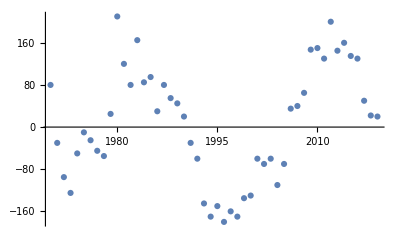

```mathematica
ListPlot[mylist2]
```

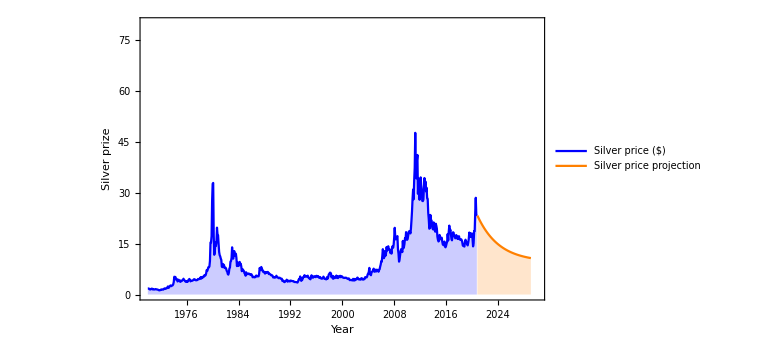
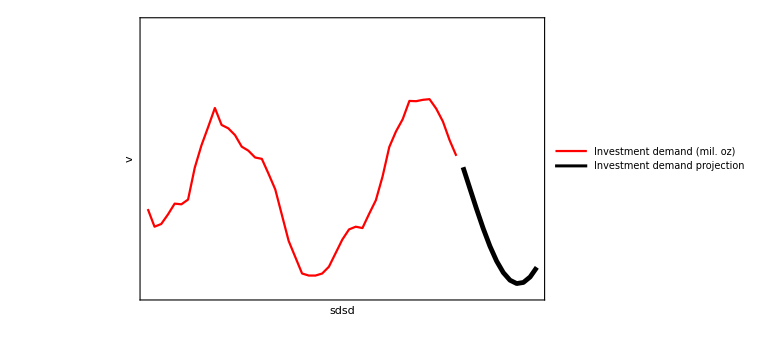

Investment_demand_proj.png

```mathematica
plot1=ListPlot[{data,forecast},PlotRange->{{1970,2030},{0,80}},PlotStyle->{Blue,Orange},ImagePadding->74, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver price ($)","Silver price projection"},{.25,.85}],FrameLabel->{"Year","Silver prize"},ImageSize->Large,BaseStyle->13,Filling->Axis];
plot2=ListPlot[{MovingAverage[mylist2,4],mylist3},PlotRange->{-200,300},PlotStyle->{Red,{Black,Thickness[.006]}},Axes->False,ImagePadding->74,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},14],Joined->True,PlotLegends->Placed[{"Investment demand (mil. oz)","Investment demand projection"},{.74,.85}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->13];
comb=Overlay[{plot1,plot2}]
Export["Investment_demand_proj.png",comb]
```

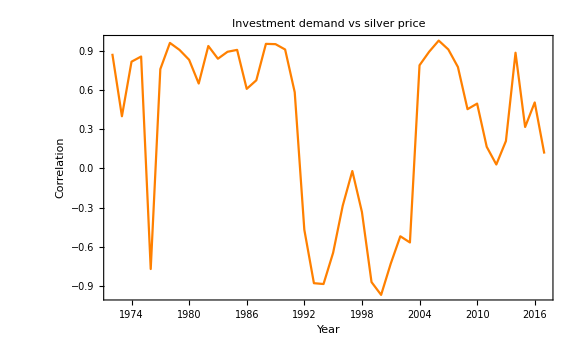

corr_invest_silver.png

```mathematica
mylist2[[20;;]];
mylist2=silverinvest1[[8;;]];
silvermonth=FF[silver,1970,1/12][[1;;]];
silveryear={};c=0;
For[i=1,i≤Length[silvermonth],i++,c=c+1;sum=sum+silvermonth[[i]][[2]];
If[c==12,silveryear=Append[silveryear,{IntegerPart[silvermonth[[i]][[1]]],sum/12}];
sum=0;
c=0;];]
silveryear;

Corr[s1_,s2_,num_,string_]:=(corr={};
For[i=1,i≤Length[s1]-num,i++,
corr=Append[corr,{s1[[i+num/2]][[1]],Correlation[s1[[i;;i+num,2]],s2[[i;;i+num,2]]]}]];
plotcorr=ListPlot[MovingAverage[corr,1],Joined->True,PlotRange->All,PlotStyle->Orange, Frame->True,Frame->True,FrameStyle->Directive[Black,14],Joined->True,FrameLabel->{"Year","Correlation"},ImageSize->Large,BaseStyle->14,PlotLabel->string,BaseStyle->Black];
Return[plotcorr];)
corr=Corr[silveryear,mylist2,4,"Investment demand vs silver price"]
Export["corr_invest_silver.png",corr]
```

{{1963.,0.},{1964.,80.},{1965.,10.},{1966.,5.},{1967.,85.},{1968.,140.},{1969.,125.},{1970.,80.},{1971.,-30.},{1972.,-95.},{1973.,-125.},{1974.,-50.},{1975.,-10.},{1976.,-25.},{1977.,-45.},{1978.,-55.},{1979.,25.},{1980.,210.},{1981.,120.},{1982.,80.},{1983.,165.},{1984.,85.},{1985.,95.},{1986.,30.},{1987.,80.},{1988.,55.},{1989.,45.},{1990.,20.},{1991.,-30.},{1992.,-60.},{1993.,-145.},{1994.,-170.},{1995.,-150.},{1996.,-180.},{1997.,-160.},{1998.,-170.},{1999.,-135.},{2000.,-130.},{2001.,-60.},{2002.,-70.},{2003.,-60.},{2004.,-110.},{2005.,-70.},{2006.,35.},{2007.,40.},{2008.,65.},{2009.,147.},{2010.,150.},{2011.,130.},{2012.,200.},{2013.,145.},{2014.,160.},{2015.,135.},{2016.,130.},{2017.,50.},{2018.,22.},{2019.,20.}}

{{1970,18.3908},{1971,1.43494},{1972,1.61411},{1973,2.44809},{1974,4.40279},{1975,4.10102},{1976,4.10776},{1977,4.39072},{1978,5.17013},{1979,11.4734},{1980,18.5327},{1981,9.56419},{1982,7.80935},{1983,11.1028},{1984,7.96363},{1985,6.04484},{1986,5.34885},{1987,6.86872},{1988,6.33752},{1989,5.31813},{1990,4.64592},{1991,3.94219},{1992,3.8698},{1993,4.35706},{1994,5.28215},{1995,5.12847},{1996,5.09305},{1997,4.93078},{1998,5.49227},{1999,5.24419},{2000,4.89438},{2001,4.35297},{2002,4.57096},{2003,4.91842},{2004,6.67882},{2005,7.32354},{2006,11.8213},{2007,13.4539},{2008,14.7948},{2009,14.8643},{2010,20.7313},{2011,35.2889},{2012,31.2828},{2013,23.3379},{2014,18.5756},{2015,15.6145},{2016,17.1284},{2017,17.1826},{2018,15.5648},{2019,16.3399}}

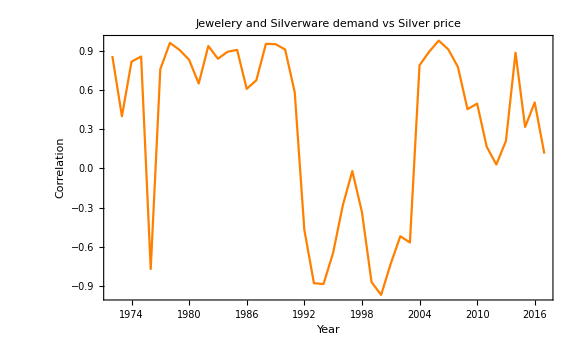

```mathematica
mylist2
silveryear
```

```mathematica
SetDirectory[NotebookDirectory[]];
industry=Import["Silver_demand.xlsx",{"Sheets","industry"}]
silvermonth=FF[silver,1970,1/12][[110;;]];
silveryear={};c=0;
For[i=1,i≤Length[silvermonth],i++,c=c+1;sum=sum+silvermonth[[i]][[2]];
If[c==12,silveryear=Append[silveryear,{IntegerPart[silvermonth[[i]][[1]]],sum/12}];
sum=0;
c=0;];]
rate=3;
industryproj={{2021,industry[[Length[industry]]][[2]]*(1-rate/100)}};
For[i=2,i≤8,i++,
industryproj=Append[industryproj,{industryproj[[i-1]][[1]]+1,industryproj[[i-1]][[2]]*(1+rate/100)}]]
```

{{1980.,375.},{1981.,370.},{1982.,380.},{1983.,375.},{1984.,440.},{1985.,400.},{1986.,460.},{1987.,450.},{1988.,480.},{1989.,500.},{1990.,520.},{1991.,580.},{1992.,600.},{1993.,660.},{1994.,680.},{1995.,720.},{1996.,750.},{1997.,760.},{1998.,820.},{1999.,800.},{2000.,920.},{2001.,860.},{2002.,850.},{2003.,860.},{2004.,920.},{2005.,930.},{2006.,850.},{2007.,860.},{2008.,850.},{2009.,800.},{2010.,820.},{2011.,840.},{2012.,800.},{2013.,830.},{2014.,850.},{2015.,870.},{2016.,890.},{2017.,920.},{2018.,930.},{2019.,940.},{2020.,950.}}

```mathematica
industryproj
```

{{2021,912.},{2022,948.48},{2023,986.419},{2024,1025.88},{2025,1066.91},{2026,1109.59},{2027,1153.97},{2028,1200.13}}

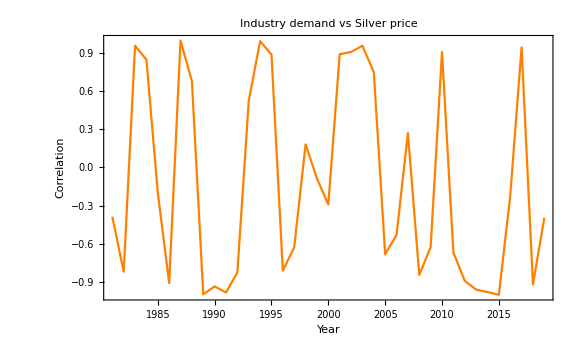

```mathematica
Corr[s1_,s2_,num_]:=(corr={};
For[i=1,i≤Length[s1]-num,i++,
corr=Append[corr,{s1[[i+num/2]][[1]],Correlation[s1[[i;;i+num,2]],s2[[i;;i+num,2]]]}]];
plotcorr=ListPlot[corr,Joined->True,PlotRange->All,PlotStyle->Orange, Frame->True,Frame->True,FrameStyle->Directive[Black,14],Joined->True,FrameLabel->{"Year","Correlation"},ImageSize->Large,BaseStyle->14,PlotLabel->"Industry demand vs Silver price",BaseStyle->Black];
Return[plotcorr];)
Corr[silveryear,industry,2]
Export["corr_industry_silver.png",Corr[silveryear,jewellery,2]];
```

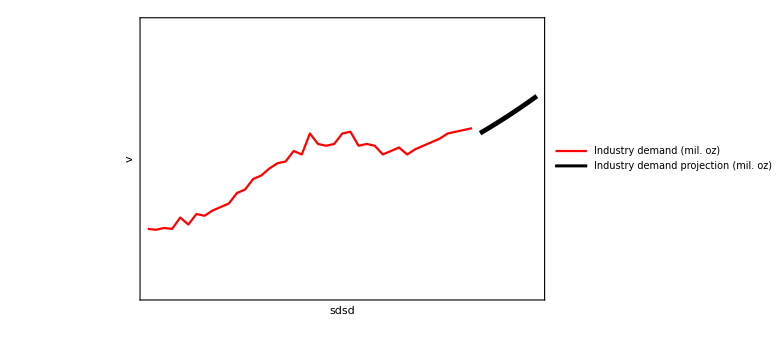
-Graphics--Graphics-

industry_demand.png

```mathematica
plot1=ListPlot[silveryear,PlotRange->{{1980,2030},{0,80}},PlotStyle->Blue,ImagePadding->74, Frame->{{True,False},{True,True}},Frame->True,FrameStyle->{{Blue,Black},{Black,Black}},Joined->True,PlotLegends->Placed[{"Silver price ($)"},{.5,.92}],FrameLabel->{"Year","Silver price"},ImageSize->Large,BaseStyle->16,Filling->Axis];
plot2=ListPlot[{industry,industryproj},PlotRange->{0,1550},PlotStyle->{Red,{Black,Thickness[.006]}},Axes->False,ImagePadding->74,Frame->{{False,True},{False,False}},FrameTicks->{{None,All},{None,None}},FrameStyle->Directive[{{Automatic,Red},{Automatic,Red}},16],Joined->True,PlotLegends->Placed[{"Industry demand (mil. oz)","Industry demand projection (mil. oz)"},{.5,.75}],FrameLabel->{"sdsd","v"},ImageSize->Large,BaseStyle->16];
comb=Overlay[{plot1,plot2}]
Export["industry_demand.png",comb]
```

```mathematica
Purchasing power analysis
```

C:\Users\adity\OneDrive - Imperial College London\Freelancing\Silver_analysis

C:\Users\adity\OneDrive - Imperial College London\Freelancing\Silver_analysis

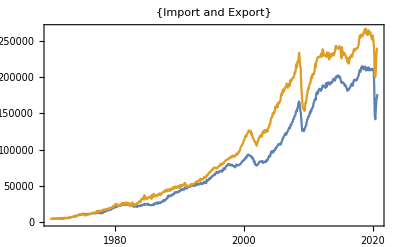

```mathematica
SetDirectory[NotebookDirectory[]]
export=Import["export.csv"][[241;;,{3,4}]];
import=Import["import.csv"][[241;;,{3,4}]];
gdp=Import["gdp.csv"][[11;;,{3,4}]];
unemp=Import["unemployment.csv"][[265;;,{3,4}]];
DateListPlot[{export,import},PlotLabel->{"Import and Export"}]
```

```mathematica
inflation[[150;;]];
```

```mathematica
realinfl;
```

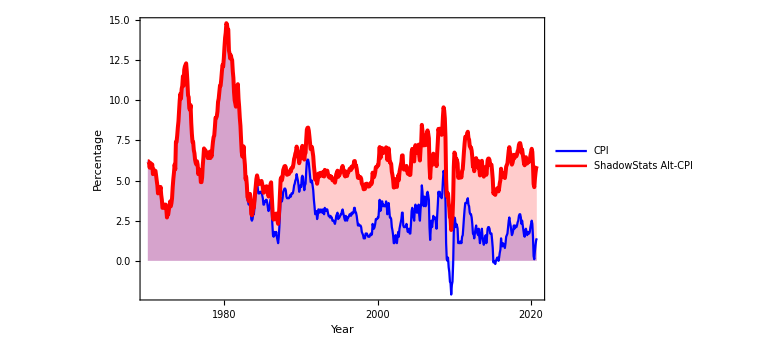

```mathematica
realinfl={};
temp=inflation;
If[temp==inflation,istart=150,istart=550];
For[i=1,i≤Length[temp],i++,
If[i≤istart,AppendTo[realinfl,{temp[[i]][[1]],temp[[i]][[2]]}],
AppendTo[realinfl,{temp[[i]][[1]],5(1-Exp[-.005(i-istart)])+temp[[i]][[2]]}];]]
plot1=DateListPlot[{temp,realinfl},PlotRange->All,PlotStyle->{{Blue},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"CPI","ShadowStats Alt-CPI"},{.7,.85}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->{Axis}]
Export["Inflation_real_shadow_stats.png",plot1]
```

```mathematica
inflation;
```

USD_purchasing_power.png

```mathematica
inflation[[1;;]];
```

{a→-0.0729031,b→148.594}

{A→2.83361,B→0.0290782,CC→0.35509}

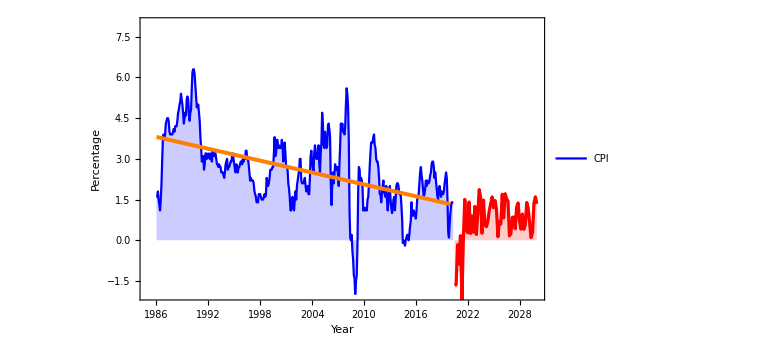

inflation_fit.png

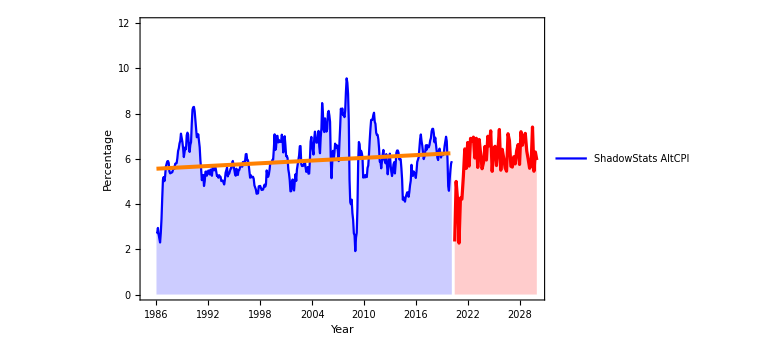

shadow_stats_inflation_fit.png

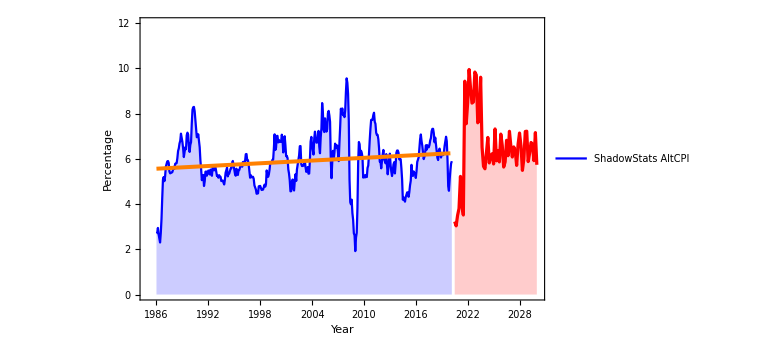

shadow_stats_inflation_maloney_fit.png

```mathematica
start=200;
year=1986;
model=a*x+b;
model2=A*Exp[-B*(x-year)+CC];

fit=FindFit[FF[inflation[[start;;]],year,1/12],model,{a,b},x]
fit2=FindFit[FF[inflation[[start;;]],year,1/12],model2,{A,B,CC},x]
mylist=Table[{i,(model/.fit)/.x->i},{i,year,2020,0.5}];
mylist2=Table[{i,(model2/.fit2)/.x->i},{i,year,2020,0.5}];

incr=2/12;

mylist30=Table[{i,If[i≤2021.5,((model/.fit)/.x->i)+RandomReal[{-4,-1}],((model/.fit)/.x->i)+RandomReal[{-1,1}]]},{i,2020.5,2030,incr}];
ListPlot[{mylist,mylist3},Joined->True,PlotRange->{0,12}];

plot1=ListPlot[{FF[inflation[[start;;]],year,1/12]},PlotRange->{{1985,2030},{-2,8}},PlotStyle->{{Blue},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"CPI","ShadowStats Alt-CPI"},{.7,.9}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->{Axis}];
plot2=ListPlot[{mylist},PlotRange->All,PlotStyle->{{Orange,Thickness[0.005]},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Linear Fit"},{.73,.8}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16];
plot3=ListPlot[{mylist30},PlotRange->All,PlotStyle->{{Red,Thickness[0.004]}}, Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Projection"},{.73,.8}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->Axis];
Show[plot1,plot2,plot3]
Export["inflation_fit.png",Show[plot1,plot2,plot3]]

model=a*x+b;
model2=A*(1-Exp[B*(x-year)+CC]);
fit=FindFit[FF[realinfl[[start;;]],year,1/12],model,{a,b},x];
fit2=FindFit[FF[realinfl[[start;;]],year,1/12],model2,{A,B,CC},x];


mylist=Table[{i,(model/.fit)/.x->i},{i,year,2020,0.5}];
mylist2=Table[{i,(model2/.fit2)/.x->i},{i,year,2020,0.5}];
mylist31=Table[{i,If[i≤2021.5,((model/.fit)/.x->i)+RandomReal[{-4,-1}],((model/.fit)/.x->i)+RandomReal[{-1,1}]]},{i,2020.5,2030,incr}];
ListPlot[{mylist,mylist31},Joined->True,PlotRange->{0,12}];

plot1=ListPlot[{FF[realinfl[[start;;]],year,1/12]},PlotRange->{{1985,2030},{0,12}},PlotStyle->{{Blue},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"ShadowStats AltCPI"},{.7,.9}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->{Axis}];
plot2=ListPlot[{mylist},PlotRange->All,PlotStyle->{{Orange,Thickness[0.005]},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Linear Fit"},{.73,.8}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16];
plot3=ListPlot[{mylist31},PlotRange->All,PlotStyle->{{Red,Thickness[0.004]}}, Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Projection"},{.73,.8}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->Axis];
Show[plot1,plot2,plot3]
Export["shadow_stats_inflation_fit.png",Show[plot1,plot2,plot3]]
mylist32=Table[{i,If[i≤2021.5,((model/.fit)/.x->i)+RandomReal[{-4,-1}],If[i≤2023.5,((model/.fit)/.x->i)+RandomReal[{4,1}],((model/.fit)/.x->i)+RandomReal[{-1,1}]]]},{i,2020.5,2030,incr}];
plot3=ListPlot[{mylist32},PlotRange->All,PlotStyle->{{Red,Thickness[0.004]}}, Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"Projection"},{.73,.8}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->Axis];
Show[plot1,plot2,plot3]
Export["shadow_stats_inflation_maloney_fit.png",Show[plot1,plot2,plot3]]



(*plot1=ListPlot[{temp,realinfl},PlotRange->All,PlotStyle->{{Blue},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"CPI","ShadowStats Alt-CPI"},{.7,.85}],FrameLabel->{"Year","Percentage"},ImageSize->Large,BaseStyle->16,Filling->{Axis}]*)
```

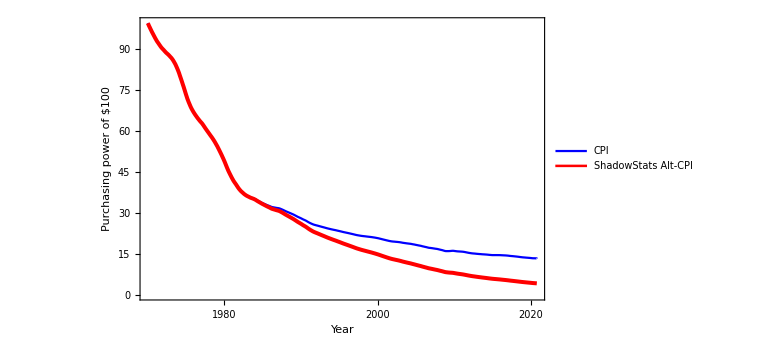

USD_purchasing_power.png

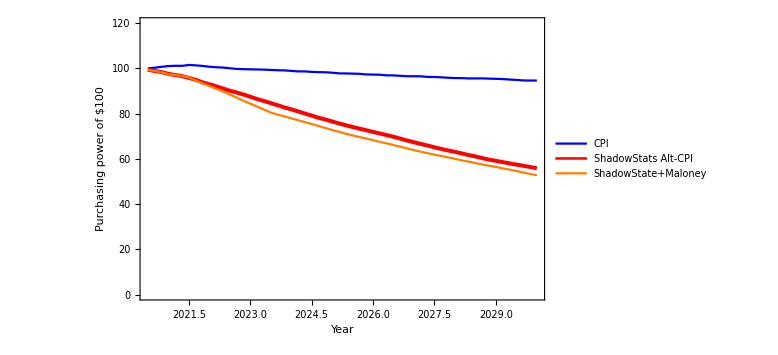

USD_purchasing_power_prediction.png

```mathematica
start=100;
infl=inflation;
For[i=1,i≤Length[infl],i++,
If[i==1,infl[[i]][[2]]=start*(1-infl[[i]][[2]]/1200),infl[[i]][[2]]=infl[[i-1]][[2]]*(1-infl[[i]][[2]]/1200)]];
shadowinfl=realinfl;
For[i=1,i≤Length[shadowinfl],i++,
If[i==1,shadowinfl[[i]][[2]]=start*(1-shadowinfl[[i]][[2]]/1200),shadowinfl[[i]][[2]]=shadowinfl[[i-1]][[2]]*(1-shadowinfl[[i]][[2]]/1200)]];

plot1=DateListPlot[{infl,shadowinfl},PlotRange->All,PlotStyle->{{Blue},{Red,Thickness[0.005]}}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"CPI","ShadowStats Alt-CPI"},{.7,.85}],FrameLabel->{"Year","Purchasing power of $100"},ImageSize->Large,BaseStyle->16]

Export["USD_purchasing_power.png",plot1]


start=100;
infl=mylist30;
For[i=1,i≤Length[infl],i++,
If[i==1,infl[[i]][[2]]=start*(1-infl[[i]][[2]]/600),infl[[i]][[2]]=infl[[i-1]][[2]]*(1-infl[[i]][[2]]/600)]];
shadowinfl=mylist31;
For[i=1,i≤Length[shadowinfl],i++,
If[i==1,shadowinfl[[i]][[2]]=start*(1-shadowinfl[[i]][[2]]/600),shadowinfl[[i]][[2]]=shadowinfl[[i-1]][[2]]*(1-shadowinfl[[i]][[2]]/600)]];
shadowinfl2=mylist32;
For[i=1,i≤Length[shadowinfl2],i++,
If[i==1,shadowinfl2[[i]][[2]]=start*(1-shadowinfl2[[i]][[2]]/600),shadowinfl2[[i]][[2]]=shadowinfl2[[i-1]][[2]]*(1-shadowinfl2[[i]][[2]]/600)]];
plot1=ListPlot[{infl,shadowinfl,shadowinfl2},PlotRange->{0,120},PlotStyle->{{Blue},{Red,Thickness[0.005]},Orange}, Frame->True,Frame->True,FrameStyle->Black,Joined->True,PlotLegends->Placed[{"CPI","ShadowStats Alt-CPI","ShadowState+Maloney"},{.7,.35}],FrameLabel->{"Year","Purchasing power of $100"},ImageSize->Large,BaseStyle->16]


Export["USD_purchasing_power_prediction.png",plot1]
```

```mathematica
mylist30;
```

```mathematica
infl
```

infl

```mathematica
func=Piecewise[{{95*Sin[(x-1963)/2.34],(x-1963)<14.7},{110*Sin[.6((x-1963)-14.7)/2.34],27>(x-1963)>14.7},{-150*Sin[.5((x-1963)-27)/2.34],41.7>(x-1963)>27},{150*Sin[.5((x-1963)-41.7)/2.34],(x-1963)>41.7}}];
mylist3=Table[{i,1.2func/.x->i},{i,2018.5,2030,1}];
```

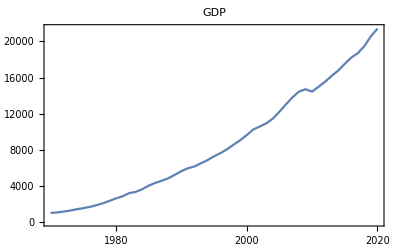

```mathematica
DateListPlot[gdp,PlotLabel->"GDP"]
```

```mathematica
DateListPlot[unemp,PlotLabel->"Unemployment"]
```

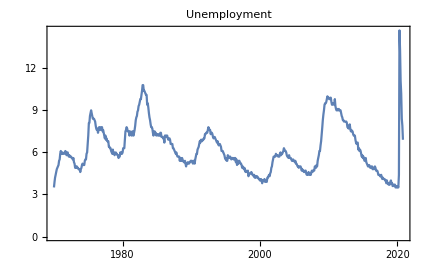

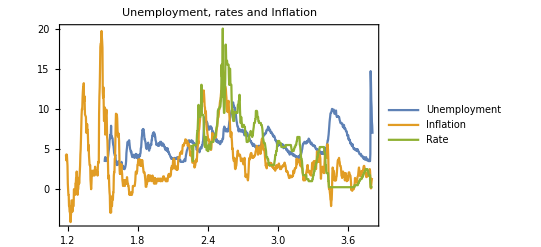

```mathematica
DateListPlot[{unemp1,inflation1,rate},PlotLabel->"Unemployment, rates and Inflation",PlotLegends->{"Unemployment","Inflation","Rate"}]
```

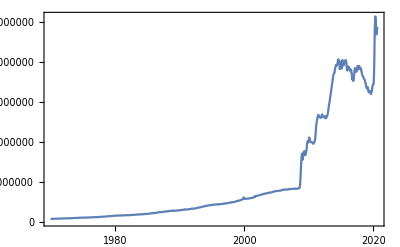

```mathematica
DateListPlot[monetary]
```

```mathematica
inflation1=Import["inflation.csv"][[2;;,{3,4}]];
unemp1=Import["unemployment.csv"][[2;;,{3,4}]];
```

```mathematica
Length[inflation1]
```

1000

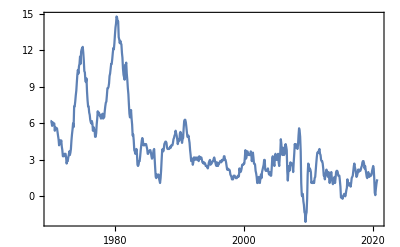

```mathematica
DateListPlot[inflation,Joined->True]
```

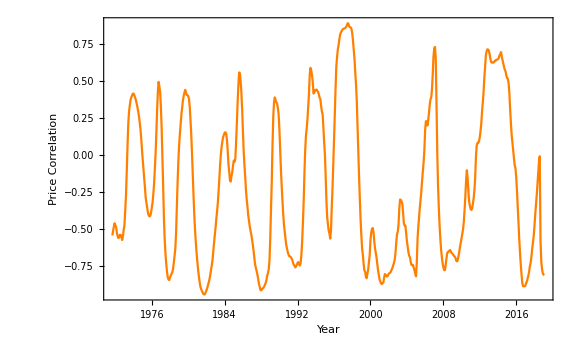

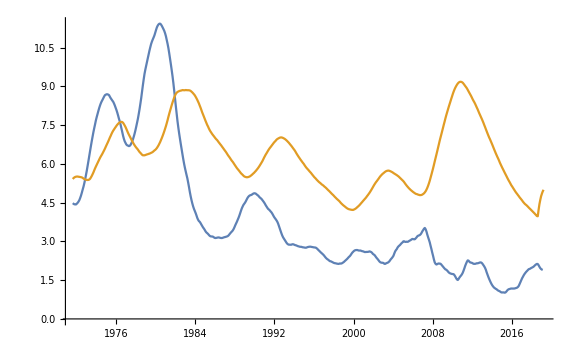

```mathematica
s1=FF[inflation,1970,1/12];
s2=FF[unemp,1970,1/12];
corr={};
num=40;
For[i=1,i≤Length[s1]-num,i++,
corr=Append[corr,{s1[[i+num/2]][[1]],Correlation[s1[[i;;i+num,2]],s2[[i;;i+num,2]]]}]]
plotcorr=ListPlot[corr,Joined->True,PlotRange->All,PlotStyle->Orange, Frame->True,Frame->True,FrameStyle->Directive[Black,14],Joined->True,FrameLabel->{"Year","Price Correlation"},ImageSize->Large,BaseStyle->14]

ListPlot[{MovingAverage[FF[inflation,1970,1/12],40],MovingAverage[FF[unemp,1970,1/12],40]},Joined->True]
```

```mathematica
Length[export]
Length[import]
```

610

610

```mathematica
;
```

```mathematica
s3=FF[export,1970,1/12];
s4=FF[import,1970,1/12];
```

```mathematica
s3-s4;
```

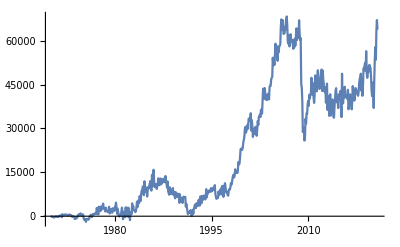

```mathematica
ListPlot[diff,Joined->True]
```

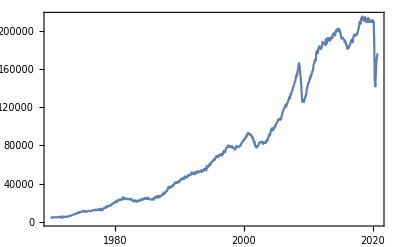

```mathematica
DateListPlot[export]
```

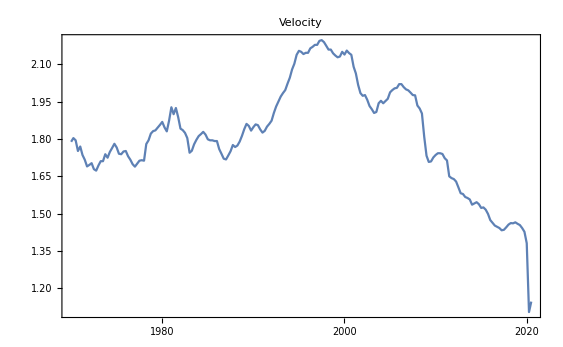

```mathematica
velocity=Import["M2V.csv"][[46;;]];
DateListPlot[velocity,PlotLabel->"Velocity"]
```

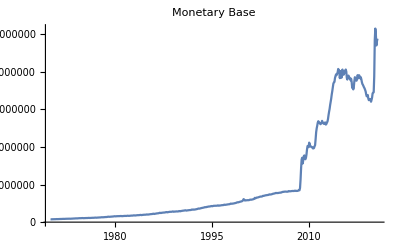

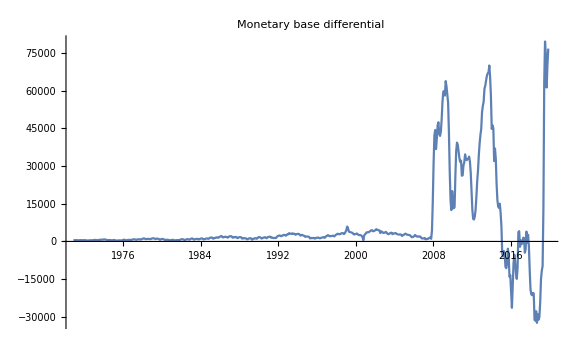

```mathematica
s5=FF[velocity,1970,3/12];
s6=FF[monetary,1970,1/12];
new={};
For[i=1,i≤Length[s6]-1,i++,
new=Append[new,{s6[[i+1]][[1]],s6[[i+1]][[2]]-s6[[i]][[2]]}]];
ListPlot[s6,Joined->True,PlotLabel->"Monetary Base"]
ListPlot[MovingAverage[new,20],Joined->True,PlotLabel->"Monetary base differential",PlotRange->All]
```

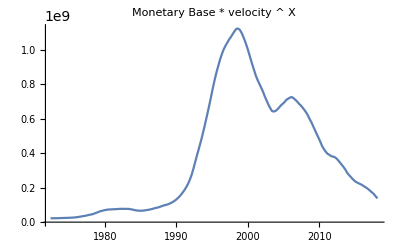

```mathematica
c=1;
new={};
X=10;
For[i=1,i≤Length[s6],i++,
If[s6[[i]][[1]]==s5[[c]][[1]],new=Append[new,{s6[[i]][[1]],s6[[i]][[2]]*s5[[c]][[2]]^X}];c=c+1;
]];

ListPlot[MovingAverage[new,20],Joined->True,PlotRange->All,PlotLabel->"Monetary Base * velocity ^ X"]
```